```mathematica
SetDirectory["~/jennaproject/data"];
```

```mathematica
kvals=Import["kvals.txt","List"][[1;;420]];
plin=Import["plin.txt","List"][[1;;420]];
b1b2=Import["b1b2.txt","List"][[1;;420]];
b1br=Import["b1br.txt","List"][[1;;420]];
b2b2=Import["b2b2.txt","List"][[1;;420]];
b2br=Import["b2br.txt","List"][[1;;420]];
brbr=Import["brbr.txt","List"][[1;;420]];
tknw=Import["tk_nowiggle.dat","Table"];
```

```mathematica
Dimensions[tknw]
Dimensions[kvals]
```

{3000,2}

{420}

```mathematica
ns=0.966;
```

### Continuous (w/ Interpolations)

```mathematica
plinfunc=Interpolation[{kvals,plin}ᵀ];
tknwfunc=Interpolation[tknw];
b1b2func=Interpolation[{kvals,b1b2+plin}ᵀ];
b1b2nw=Fit[{kvals[[1;;420;;5]],(b1b2+plin)[[1;;420;;5]]}ᵀ,{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^5,Log[x]^6,Log[x]^7,Log[x]^8},x];
b1brfunc=Interpolation[{kvals,b1br+plin}ᵀ];
b1brnw=Fit[{kvals[[1;;420;;5]],(b1br+plin)[[1;;420;;5]]}ᵀ,{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^5,Log[x]^6,Log[x]^7,Log[x]^8},x];
b2b2func=Interpolation[{kvals,b2b2+plin}ᵀ];
b2b2nw=Fit[{kvals[[1;;420;;5]],(b2b2+plin)[[1;;420;;5]]}ᵀ,{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^5,Log[x]^6,Log[x]^7,Log[x]^8},x];
b2brfunc=Interpolation[{kvals,b2br+plin}ᵀ];
b2brnw=Fit[{kvals[[1;;420;;5]],(b2br+plin)[[1;;420;;5]]}ᵀ,{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^5,Log[x]^6,Log[x]^7,Log[x]^8},x];
brbrfunc=Interpolation[{kvals,brbr+plin}ᵀ];
brbrnw=Fit[{kvals[[1;;420;;5]],(brbr+plin)[[1;;420;;5]]}ᵀ,{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^5,Log[x]^6,Log[x]^7,Log[x]^8},x];
```

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

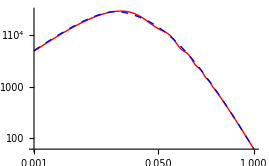

```mathematica
psnwfunc[k_]:=4.0*10^6*k^ns*tknwfunc[k]^2;
LogLogPlot[{plinfunc[k],psnwfunc[k]},{k,0.001,1},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}]
```

```mathematica
ϕ12=ListLogLogPlot[{kvals,(plin+b1b2)}ᵀ,PlotStyle->Thick];
ω12=LogLogPlot[b1b2nw,{x,0.005,.3},PlotStyle->Red];
```

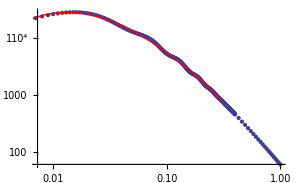

```mathematica
ϕ1r=ListLogLogPlot[{kvals,(plin+b1br)}ᵀ,PlotStyle->Thick];
ω1r=LogLogPlot[b1brnw,{x,0.005,.3},PlotStyle->Red];
Show[ϕ1r,ω1r]
```

```mathematica
LogLogPlot[plinfunc[k]/psnwfunc[k],{k,0.005,0.3}];
LogLogPlot[b1b2func[k]/psnwfunc[k],{k,0.005,0.3}];
LogLogPlot[b2b2func[k]/psnwfunc[k],{k,0.005,0.3}];
LogLogPlot[b1brfunc[k]/psnwfunc[k],{k,0.005,0.3}];
LogLogPlot[b2brfunc[k]/psnwfunc[k],{k,0.005,0.3}];
LogLogPlot[brbrfunc[k]/psnwfunc[k],{k,0.005,0.3}];
```

InterpolatingFunction::dmval: Input value {-5.298233724937694`} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
LogLogPlot[plinfunc[x]/psnwfunc[x],{x,0.005,0.3}];
LogLogPlot[b1b2func[x]/b1b2nw,{x,0.005,0.3}];
LogLogPlot[b2b2func[x]/b2b2nw,{x,0.005,0.3}];
LogLogPlot[b1brfunc[x]/b1brnw,{x,0.005,0.3}];
LogLogPlot[b2brfunc[x]/b2brnw,{x,0.005,0.3}];
LogLogPlot[brbrfunc[x]/brbrnw,{x,0.005,0.3}];
```

InterpolatingFunction::dmval: Input value {-5.298233724937694`} lies outside the range of data in the interpolating function. Extrapolation will be used.

### Discrete (w/ data)

```mathematica
psnw=psnwfunc[#]&/@kvals;
```

```mathematica
mark1=Graphics[{Blue,Disk[]}];
mark2=Graphics[{Red,Disk[]}];
mark3=Graphics[{Orange,Disk[]}];
```

```mathematica
ListLogLogPlot[{{kvals,psnw}ᵀ,{kvals,plin}ᵀ},PlotMarkers->{{mark1,.02},{mark2,.015}}];
```

```mathematica
ListPlot[{kvals,plin-psnw}ᵀ,PlotMarkers->{mark3,.02},Joined->True];
```

```mathematica
ListPlot[{kvals,b1b2-psnw}ᵀ,PlotMarkers->{mark3,.02},Joined->True];
ListPlot[{kvals,b1br-psnw}ᵀ,PlotMarkers->{mark3,.02},Joined->True];
ListPlot[{kvals,b2b2-psnw}ᵀ,PlotMarkers->{mark3,.02},Joined->True];
ListPlot[{kvals,b2br-psnw}ᵀ,PlotMarkers->{mark3,.02},Joined->True];
ListPlot[{kvals,brbr-psnw}ᵀ,PlotMarkers->{mark3,.02},Joined->True];
```